```mathematica
Clear["Global`*"]
```

```mathematica
U[x_]:=If[x<0 ,0,V]
```

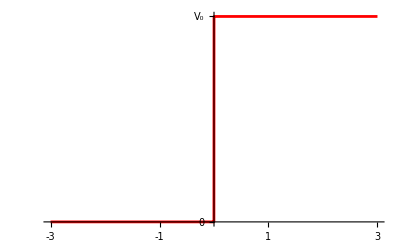

```mathematica
Plot[U[x]/.V->1,{x,-3,3}, PlotStyle->{{Hue[1.0],Thickness[0.005]}}, PlotRange->All,Ticks->{{-3,-2,-1,0,1,2,3},{{0,0},{1,Subscript[V, 0]}}}]
```

Time Independent Schrödinger equation is

```mathematica
sch=-ℏ^2/(2 m)ψ''[x]+V[x]ψ[x]==En ψ[x]
```

V[x] ψ[x]-(ℏ^2 ψ''[x])/(2 m)==En ψ[x]

```mathematica
eq1=Solve[sch,ψ''[x]][[1,1]]//Simplify
```

ψ''[x]→(2 m (-En+V[x]) ψ[x])/ℏ^2

For the region x<0, V(x)=0

```mathematica
eq2=eq1/.V[x]->0
```

ψ''[x]→-(2 En m ψ[x])/ℏ^2

```mathematica
krule=En->(k^2 ℏ^2)/(2m)
```

En→(k^2 ℏ^2)/(2 m)

```mathematica
eq3=eq2/.krule/.Rule->Equal
```

ψ''[x]==-k^2 ψ[x]

The most general solution is

```mathematica
Subscript[ψ, 1][x]==A ⅇ^(ⅈ k x)+B ⅇ^(-ⅈ k x);
```

The first term represent incident wave and second term represent reflected wave from step. So, we can separate this equation as,

```mathematica
ψinc[x_]=ⅇ^(ⅈ k x);
ψrefl[x_]=R ⅇ^(-ⅈ k x);
```

Here R is reflection coefficient.

For the region x>0, V(x)>0

```mathematica
qrule=V[x]-En->(q^2 ℏ^2)/(2m)
```

-En+V[x]→(q^2 ℏ^2)/(2 m)

```mathematica
eq4=eq1/.qrule
```

ψ''[x]→q^2 ψ[x]

The most general solution is

```mathematica
Subscript[ψ, 2][x]==C ⅇ^(ⅈ k x)+D ⅇ^(-ⅈ k x);
```

Here there no chance of reflection . ie, D=0.
So, we can write this equation as

```mathematica
ψtran[x_]=T ⅇ^(ⅈ q x);
```

Here T is transmission coefficient. 

In Short,

```mathematica
ψinc[x_]=ⅇ^(ⅈ k x);
ψrefl[x_]=R ⅇ^(-ⅈ k x);
ψtran[x_]=T ⅇ^(ⅈ q x);
```

krule and qrule together

```mathematica
ks={k->√(2 m En)/ℏ,q->√(2 m (En-V))/ℏ}; (* New *)
```

Now apply boundary condition

```mathematica
bc={(ψinc[x]+ψrefl[x]-ψtran[x]/.x->0)==0,(D[ψinc[x]+ψrefl[x],x]-D[ψtran[x] ,x]/.x->0)==0}//Simplify
```

{1+R==T,k R+q T==k}

Solve for R & T

```mathematica
RandT=Solve[bc,{R,T}][[1]]
```

{R→-(-k+q)/(k+q),T→(2 k)/(k+q)}

To plot the curve, assume m & ℏ as a constant

```mathematica
values={m->1,ℏ->1};
```

```mathematica
plotψ[wave_,V0_,E0_,thickness_,col_,xrange_]:=Plot[Re[wave/.RandT/.ks/.values/.V->V0/.En->E0],xrange,PlotStyle->{Hue[col],Thickness[thickness]},PlotRange->{{-12,12} ,{-3.5,3.5}},AxesStyle->Transparent]
```

```mathematica
wave2D[ V0_,E0_,xmin_,xmax_]:=Show[{plotψ[(ψinc[x]+ψrefl[x]),V0,E0,0.003,0.3,{x,xmin,0}],plotψ[ψtran[x],V0,E0,0.003,0.9,{x,0,xmax}]},Graphics[{Thickness[.005],RGBColor[1,0,0],{Line[{{0,3},{0,0}}],Line[{{xmin,0},{0,0}}],Line[{{xmax,3},{0,3}}]}}]]
```

```mathematica
Manipulate[wave2D[V0,E0,-12,12],{{V0,1,"Step Potential, V_0"},1,5,0.5,Appearance->"Labeled"},{{E0,0.5,"Particle Energy, E"},0.01,5,0.01,Appearance->"Labeled"}]
```